```mathematica
m = 1
M = 20
G = 6.67*10^-11
R = 1
```

1

20

6.67×10^-11

1

```mathematica
k = m/M
lambda = k/(1+k)
omega = (G*M / (R^3 * (1 - lambda)))^(0.5)
rm = (1-lambda)*R
rM = lambda*R
```

1/20

1/21

0.0000374259

20/21

1/21

```mathematica
S = ( y^2 + (x +lambda*R)^2)^0.5
s = ( y^2 + ( x - (1-lambda)*R)^2)^0.5
```

((1/11+x)^2+y^2)^0.5

((-10/11+x)^2+y^2)^0.5

```mathematica
U0 = -2(1 - lambda)*R/S - 2*lambda * R/s - (x^2 + y^2)/R^2
```

-x^2-y^2-2/(21 ((-10/11+x)^2+y^2)^0.5)-40/(21 ((1/11+x)^2+y^2)^0.5)

```mathematica
-x^2-y^2-2/(11 ((-10/11+x)^2+y^2)^0.5)-20/(11 ((1/11+x)^2+y^2)^0.5)
```

-x^2-y^2-2/(11 ((-10/11+x)^2+y^2)^0.5)-20/(11 ((1/11+x)^2+y^2)^0.5)

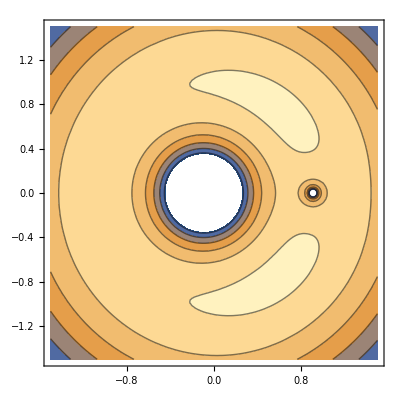

```mathematica
ContourPlot[U0,{x,-1.5,1.5},{y,-1.5,1.5}]
```

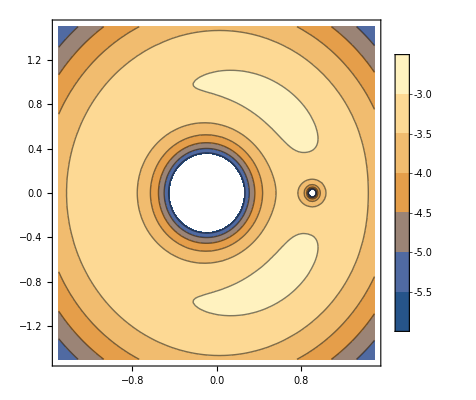

Drop::normal: Nonatomic expression expected at position 1 in Drop[U,1].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Drop[U,1].

Hold[Drop[U,1]]

Syntax::sntxf: "t⟦" cannot be followed by "2:4⟧".

```mathematica
ContourPlot[U0,{x,-1.5,1.5},{y,-1.5,1.5},PlotLegends->Automatic]
```